# Q2

x | -5. | -4.9 | -4.8 | -4.7 | -4.6 | -4.5 | -4.4 | -4.3 | -4.2 | -4.1 | -4. | -3.9 | -3.8 | -3.7 | -3.6 | -3.5 | -3.4 | -3.3 | -3.2 | -3.1 | -3. | -2.9 | -2.8 | -2.7 | -2.6 | -2.5 | -2.4 | -2.3 | -2.2 | -2.1 | -2. | -1.9 | -1.8 | -1.7 | -1.6 | -1.5 | -1.4 | -1.3 | -1.2 | -1.1 | -1. | -0.9 | -0.8 | -0.7 | -0.6 | -0.5 | -0.4 | -0.3 | -0.2 | -0.1 | 0. | 0.1 | 0.2 | 0.3 | 0.4 | 0.5 | 0.6 | 0.7 | 0.8 | 0.9 | 1. | 1.1 | 1.2 | 1.3 | 1.4 | 1.5 | 1.6 | 1.7 | 1.8 | 1.9 | 2. | 2.1 | 2.2 | 2.3 | 2.4 | 2.5 | 2.6 | 2.7 | 2.8 | 2.9 | 3. | 3.1 | 3.2 | 3.3 | 3.4 | 3.5 | 3.6 | 3.7 | 3.8 | 3.9 | 4. | 4.1 | 4.2 | 4.3 | 4.4 | 4.5 | 4.6 | 4.7 | 4.8 | 4.9 | 5.
f[x] | 0.00366559 | 0.00272902 | 0.00143467 | -0.000225339 | -0.00224045 | -0.00457822 | -0.00718123 | -0.00996471 | -0.0128152 | -0.0155904 | -0.0181207 | -0.0202124 | -0.0216531 | -0.0222192 | -0.021686 | -0.0198393 | -0.0164902 | -0.0114906 | -0.0047508 | 0.00374311 | 0.0139113 | 0.0255639 | 0.0383874 | 0.051934 | 0.0656173 | 0.0787133 | 0.09037 | 0.0996263 | 0.105441 | 0.10673 | 0.102422 | 0.0915147 | 0.0731481 | 0.0466831 | 0.0117855 | -0.0314881 | -0.0826071 | -0.140491 | -0.203446 | -0.269125 | -0.334512 | -0.395937 | -0.449137 | -0.48936 | -0.511514 | -0.510378 | -0.480858 | -0.418297 | -0.318829 | -0.179763 | 0. | 0.219564 | 0.475637 | 0.762188 | 1.07017 | 1.38735 | 1.69829 | 1.98445 | 2.22459 | 2.39528 | 2.47173 | 2.42886 | 2.24262 | 1.89153 | 1.35844 | 0.632456 | -0.289129 | -1.39882 | -2.67709 | -4.09082 | -5.59206 | -7.11744 | -8.58822 | -9.91126 | -10.9809 | -11.6821 | -11.8946 | -11.4985 | -10.381 | -8.44375 | -5.61221 | -1.84441 | 2.85925 | 8.44671 | 14.8057 | 21.7564 | 29.0468 | 36.3503 | 43.2672 | 49.3305 | 54.0171 | 56.764 | 56.9901 | 54.1249 | 47.642 | 37.0977 | 22.1741 | 2.72399 | -21.1825 | -49.2144 | -80.7399

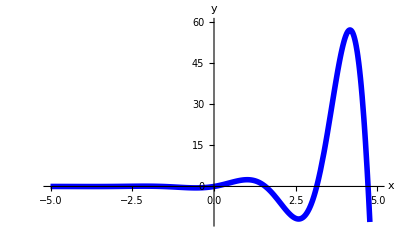

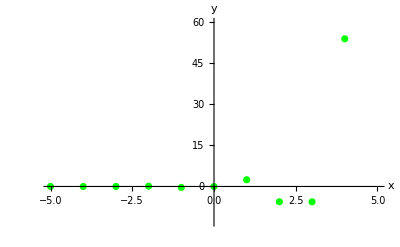

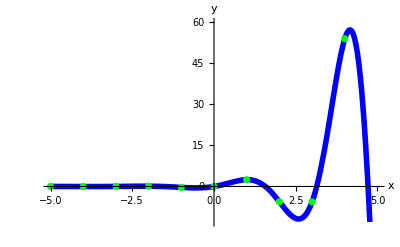

```mathematica
f[x_]= E^x*Sin[2x];
(*i*)
list = TableForm[
{
Table[x,{x,-5,5,0.1}],
Table[f[x],{x,-5,5,0.1}]
},
TableHeadings->{{"x","f[x]"}}
]
(*ii*)
p1 = Plot[
f[x],{x,-5,5},
PlotRange->{{-5,5},{-13,60}},
AxesLabel->{x,y},
PlotStyle->{RGBColor[0,0,1],Thickness[0.01]}
]
p2 = ListPlot[
Table[
{x,f[x]},
{x,-5,5}],
PlotRange->{{-5,5},{-13,60}},
AxesLabel->{x,y},
PlotStyle->{RGBColor[0,1,0],Thickness[0.02]}
]
Show[p1,p2]
```